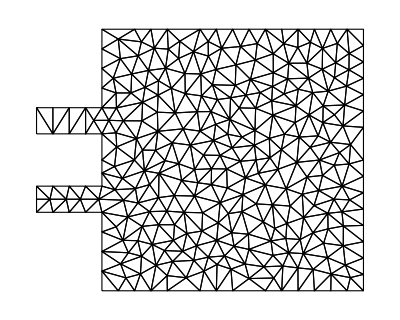

```mathematica
(* Start of given code *)
slits={Rectangle[{-0.25,0.3},{0, 0.4}],Rectangle[{-0.25,0.6},{0, 0.7}]};
square=Rectangle[{0,0},{1,1}];
Ω=RegionUnion[slits⟦1⟧,slits⟦2⟧,square];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω, "MeshOrder"-> 1];
mesh["Wireframe"]
(*Remove semicolon for more detailed mesh*)
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]];
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"]⟦1,1⟧;
boundary =Flatten[mesh["BoundaryElements"]⟦1,1⟧];
boundary=DeleteDuplicates[boundary];
Subscript[Γ, D]=Cases[nodes⟦boundary⟧,{x_,_}/;x== -0.25];
boundNodes = Flatten[Nearest[nodes->"Index",Subscript[Γ, D],1]];
(* End of given code *)
```

```mathematica
(* Standard basis functions, i.e. shape functions *)
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
gradψ=Transpose@Grad[{Subscript[ψ, 0][{ξ,η}],Subscript[ψ, 1][{ξ,η}],Subscript[ψ, 2][{ξ,η}]},{ξ,η}];
gradψT=Transpose@gradψ;
innerMass=Integrate[
Table[Subscript[ψ, i][{ξ,η}]Subscript[ψ, j][{ξ,η}],{i,0,2},{j,0,2}],
{ξ,0,1},{η,0,1-ξ}];

(* The Jacobian and Jacobian inverse *)
(* Here we utilise the fact that R^2 vectors are represented as lists and we can directly get their "transpose" by using the list *)
J[elementNodes_?MatrixQ]:={
elementNodes⟦2⟧-elementNodes⟦1⟧,
elementNodes⟦3⟧-elementNodes⟦1⟧}
B[elementNodes_?MatrixQ]:={
{elementNodes⟦3,2⟧-elementNodes⟦1,2⟧,elementNodes⟦1,2⟧-elementNodes⟦2,2⟧},
{elementNodes⟦1,1⟧-elementNodes⟦3,1⟧,elementNodes⟦2,1⟧-elementNodes⟦1,1⟧}}

(* The local stiffness matrix *)
(* Formally, we would have to do something like this 
localStiffness[nodes_, element_]:=
1/(Det@J[nodes,element])NIntegrate[gradψT.(Transpose@B[nodes,element]).B[nodes,element].gradψ,{ξ,0,1},{η,0,1-ξ}]*)
(* However the integrand is constant so we just need to multiply it by the area of the standard triangle, which is 1/2 *)
localStiffness[elementNodes_?MatrixQ]:=
0.5/(Abs@Det@J[elementNodes])gradψT.Transpose@B[elementNodes].B[elementNodes].gradψ
(* Same comments apply to localMass *)
localMass[elementNodes_?MatrixQ]:=0.5Abs@Det@J[elementNodes]innerMass


FEMMatrix[nodes_?ListQ,elements_?ListQ,localFunction_,nullNodes_:{}?ListQ]:=Module[{
globalMatrix = ConstantArray[0,{Length@nodes,Length@nodes}], element, quality},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
quality=localFunction@nodes⟦element⟧;
For[i=1,i≤Length@element,i++,
For[j=1,j≤Length@element,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=quality⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_:{}?ListQ]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The function that assebles the global mass matrix *)
massMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_:{}?ListQ]:=FEMMatrix[nodes,elements,localMass,nullNodes]
```

```mathematica
(* Obviously b is the zero vector and so we remove it from consideration from now on *)
(* dirichletNodeFunctions is a list of pairs of nodes and function) - each set of nodes has its corresponding function to give it values in the recurrence relation *)
solveEquation[nodes_?ListQ,elements_?ListQ,dirichletNodeFunctions_?ListQ,T_?NumberQ,τ_?NumberQ]:=Module[{
n=Length@nodes,timeSteps=Ceiling@(T/τ),
mass,stiffness,In,leftMatrix,rightMatrix,
dirichletNodes=First/@dirichletNodeFunctions,sol},
mass=massMatrix[nodes,elements,dirichletNodes];
stiffness=stiffnessMatrix[nodes,elements,{}];
In=IdentityMatrix[n];
leftMatrix=Join[
Table[Join[In⟦k⟧,-τ/2 In⟦k⟧],{k,1,n}],
Table[Join[τ/2 stiffness⟦k⟧,mass⟦k⟧],{k,1,n}]
];
rightMatrix=Join[
Table[Join[In⟦k⟧,τ/2 In⟦k⟧],{k,1,n}],
Table[Join[-τ/2 stiffness⟦k⟧,mass⟦k⟧],{k,1,n}]
]; 
sol=ConstantArray[0,{timeSteps, 2n}];
(* We also assume u'(0, x̄) = 0 *)

For[k=2,k<timeSteps,k++,
sol⟦k+1⟧=LinearSolve[leftMatrix,rightMatrix.sol⟦k⟧];

(* Take into account the dirichlet conditions *)
For[i=1,i≤Length@dirichletNodeFunctions,i++,
{someNodeIndexes, someFunction}=dirichletNodeFunctions⟦i⟧;
sol⟦k+1, someNodeIndexes⟧=someFunction[nodes⟦#⟧,k τ]&/@someNodeIndexes;
];
];

(* Return only the q component of the solution *)
Take[#,n]&/@sol
]
```

```mathematica
(* Solve the equation *)
T=2;
τ=0.005;
boundaryPeriodicFunction[{x_,y_},t_]:=0.1Sin[8Pi t]
q=solveEquation[nodes,elements,{{boundNodes,boundaryPeriodicFunction}},T,τ];
u=Table[Interpolation[Thread[{nodes,q⟦k⟧}],InterpolationOrder->1],{k,1,Length@q}];
```

```mathematica
(* The maximum displacement of any point from z=0 *)
maxDisp=MaxValue[{boundaryPeriodicFunction[{x,y},t],0≤t≤2,{x,y}∈Ω},{x,y,t}];
minDisp =MinValue[{boundaryPeriodicFunction[{x,y},t],0≤t≤2,{x,y}∈Ω},{x,y,t}];
```

```mathematica
(* 3D plot of the solution as it is appropriate for a wave equation *)
Manipulate[
Plot3D[
{u⟦k⟧[x,y]},
{x,y}∈Ω,
PlotLabel->"3D plot of u",PlotRange->{1.2 minDisp,1.2maxDisp}],
{k,1,Length@u,1}
]
```